```mathematica
(* baseed on https://syntacticsalt.com/blog/2016-03-07-solving-sudoku-via-sat.html *)
ClearAll["Global`*"];
W=4;U=W^2;

ShowMarking[marking_]:=Module[{},Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,If[KeyExistsQ[marking,{i,j}],Text[Style[marking[{i,j}],Medium],{i+0.5,j+0.5}]]},{i,1,U},{j,1,U}]]]

ShowSolution[soln_]:=Module[{arr,r},
arr=ArrayReshape[soln,{U,U,U}];
r=Table[Flatten[Position[arr⟦i,j⟧,True]]⟦1⟧,{i,U},{j,U}];
Graphics[Table[{EdgeForm[Thin],If[EvenQ[Floor[(j-1)/W]+Floor[(i-1)/W]],White,Lighter[Gray,0.5]],Rectangle[{i,j},{i+1,j+1}],Black,Text[Style[r⟦i,j⟧,Medium],{i+0.5,j+0.5}]},{i,1,U},{j,1,U}]]]

s=Table[Table[Table[Unique[s],{z,1,U}],{y,1,U}],{x,1,U}];
AndList[l_]:=Fold[And,True,l];
OrList[l_]:=Fold[Or,False,l];

(* Sudoku rules constraints *)

f1=AndList[Table[AndList[Table[OrList[Table[s⟦x,y,i⟧,{i,1,U}]],{x,1,U}]],{y,1,U}]];
f2=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦x,y,z⟧]||Not[s⟦i,y,z⟧],{i,x+1,U}]],{x,1,U-1}]],{z,1,U}]],{y,1,U}]];
f3=AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦x,y,z⟧]||Not[s⟦x,i,z⟧],{i,y+1,U}]],{y,1,U-1}]],{z,1,U}]],{x,1,U}]];
f4=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+x,W j+k,z⟧],{k,y+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
f5=AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[AndList[Table[Not[s⟦W i+x,W j+y,z⟧]||Not[s⟦W i+k,W j+l,z⟧],{l,1,W}]],{k,x+1,W}]],{y,1,W}]],{x,1,W}]],{j,0,W-1}]],{i,0,W-1}]],{z,1,U}]];
```

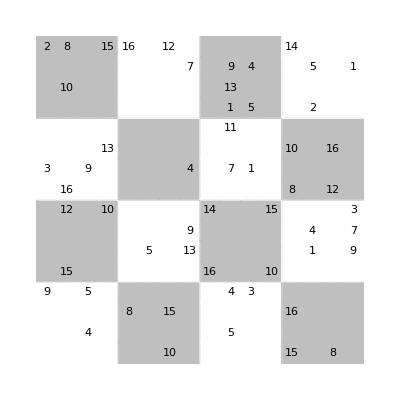

constraint set size: 92416

known problem clues: 55

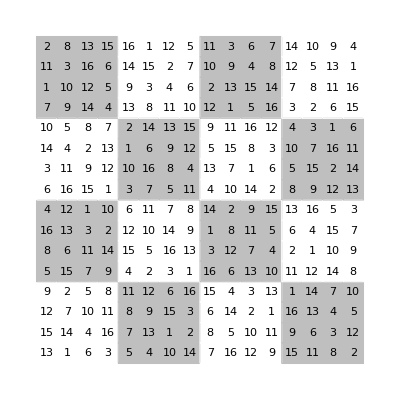

That took 4.67188 seconds.

```mathematica
(* convert matrix to Association form *)
GetAssociationRules[m_?MatrixQ]:=Association@@Reap[With[{b=Dimensions[m]},
Do[If[m⟦i,j⟧≠0,Sow[{i,j}->m⟦i,j⟧]],{i,b⟦1⟧},{j,b⟦2⟧}]]]⟦2⟧;

mymat={
{0,0,0,9,0,0,0,0,0,3,0,0,0,0,0,2},{0,0,0,0,15,0,0,12,16,0,0,0,0,10,0,8},{0,4,0,5,0,0,0,0,0,9,0,0,0,0,0,0},{0,0,0,0,0,0,0,10,0,0,13,0,0,0,0,15},{0,0,8,0,0,0,0,0,0,0,0,0,0,0,0,16},{0,0,0,0,0,5,0,0,0,0,0,0,0,0,0,0},{10,0,15,0,0,0,0,0,0,0,0,0,0,0,0,12},{0,0,0,0,0,13,9,0,0,4,0,0,0,0,7,0},{0,0,0,0,16,0,0,14,0,0,0,0,0,0,0,0},{0,5,0,4,0,0,0,0,0,7,0,11,1,13,9,0},{0,0,0,3,0,0,0,0,0,1,0,0,5,0,4,0},{0,0,0,0,10,0,0,15,0,0,0,0,0,0,0,0},{15,0,16,0,0,0,0,0,8,0,10,0,0,0,0,14},{0,0,0,0,0,1,4,0,0,0,0,0,2,0,5,0},{8,0,0,0,0,0,0,0,12,0,16,0,0,0,0,0},{0,0,0,0,0,9,7,3,0,0,0,0,0,0,1,0}};

initial=GetAssociationRules[mymat];
fInit=AndList[Map[s⟦#⟦1⟧,#⟦2⟧,initial[#]⟧&,Keys[initial]]];
ShowMarking[initial]
Print["constraint set size: "<>ToString[Length[Flatten[f1&&f2&&f3&&f4&&f5]]]];
Print["known problem clues: "<>ToString[Length[initial]]];
soln=Timing[SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&fInit,Flatten[s]]];
(* r=ArrayReshape[soln,{U,U,U}];
Table[Table[Flatten[Position[r[[i,j]],True]][[1]],{j,1,U}],{i,1,U}]//TableForm *)
ShowSolution[soln⟦2⟧]
Print["That took "<>ToString[soln⟦1⟧]<>" seconds."];
```

Need to create routines for:
	1. convert puzzle to canonical form
	2. search for minimal clue puzzles
		a. remove two, insert one until only one solution exists
	3. database search
		a. special case for puzzles with < 256 states: single line per solution
		b. more general database
	4. ?

```mathematica
(* assume starting puzzle has been solved by above solver, now we want to find other puzzles with fewer clues,
	1. add rules until solvable,
		a. check clues < best,
		b. check solution count is one,
		c. check solution non-dupe,
			print "dupe, but better",
		d. output problem,
	2. remove clues until two under best,
	3. loop to 1.
*)
Block[{workclues,cluesum,temp,atempts,aclues,i,j,k,n,x,y,r,arr},
workclues = Normal[initial];
cluesum=Length[workclues]; (* reduce this amount *)
atempts=0;
While[True,
(* try sudoku, finding two instances quicker than total count. since SatisfiabilityInstances[] cannot include multiple solutions in the general case one must get a solution and then exclude that solution with another clause *)
atempts++;
aclues=Association[workclues];
soln=SatisfiabilityInstances[f1&&f2&&f3&&f4&&f5&&AndList[Map[s⟦#⟦1⟧,#⟦2⟧,aclues[#]⟧&,Keys[aclues]]],Flatten[s]];
(* success? *)
If[Length[soln]== 1,
(* exclude that solutions and try to find another *)
arr=ArrayReshape[soln,{U,U,U}];
r=Table[Flatten[Position[arr⟦i,j⟧,True]]⟦1⟧,{i,U},{j,U}];
(* create rules for positions filled *)
arr=Reap[Do[If[Count[workclues,{i,j}->r⟦i,j⟧]==0,
Sow[s⟦i,j,r⟦i,j⟧⟧]],{i,1,U},{j,1,U}]]⟦2,1⟧;

soln=SatisfiabilityInstances[Not[AndList[arr]]&&f1&&f2&&f3&&f4&&f5&&AndList[Map[s⟦#⟦1⟧,#⟦2⟧,aclues[#]⟧&,Keys[aclues]]],Flatten[s]];

If[Length[soln]≠1,
(* only one solution *NEW*)
cluesum=Length[workclues];
Print[{Length[workclues],workclues}]];
];
(* add random rules *)
While[Length[workclues]≤cluesum,j=1;
While[j≠0,
n=RandomInteger[{1,U}];
x=RandomInteger[{1,U}];
y=RandomInteger[{1,U}];
j=Count[workclues,{x,y}->_]
+Count[workclues,{x,_}->n]
+Count[workclues,{_,y}->n]
+Count[workclues,{a_,b_}->n/;Mod[a,W]==Mod[x,W]&&Mod[b,W]==Mod[y,W]];
];AppendTo[workclues,{x,y}->n]
(*NotebookDelete[temp];
PrintTemporary[ToString[Length[workclues]]<>" atempts "<>ToString[atempts]<>", adding "<>ToString[{x,y}->n]];*)
];
(* remove clues randomly *)
While[Length[workclues]≥cluesum,
workclues=ReplacePart[workclues,RandomInteger[{1,Length[workclues]}]->Nothing]];
]];
```

{55,{{1,4}→9,{1,10}→3,{1,16}→2,{2,5}→15,{2,8}→12,{2,9}→16,{2,14}→10,{2,16}→8,{3,2}→4,{3,4}→5,{3,10}→9,{4,8}→10,{4,11}→13,{4,16}→15,{5,3}→8,{5,16}→16,{6,6}→5,{7,1}→10,{7,3}→15,{7,16}→12,{8,6}→13,{8,7}→9,{8,10}→4,{8,15}→7,{9,5}→16,{9,8}→14,{10,2}→5,{10,4}→4,{10,10}→7,{10,12}→11,{10,13}→1,{10,14}→13,{10,15}→9,{11,4}→3,{11,10}→1,{11,13}→5,{11,15}→4,{12,5}→10,{12,8}→15,{13,1}→15,{13,3}→16,{13,9}→8,{13,11}→10,{13,16}→14,{14,6}→1,{14,7}→4,{14,13}→2,{14,15}→5,{15,1}→8,{15,9}→12,{15,11}→16,{16,6}→9,{16,7}→7,{16,8}→3,{16,15}→1}}

$Aborted